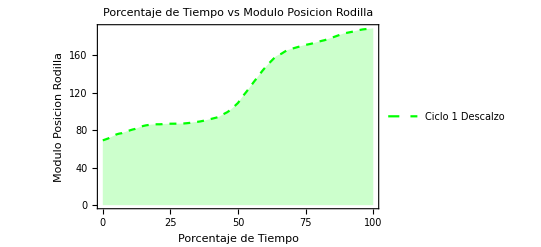

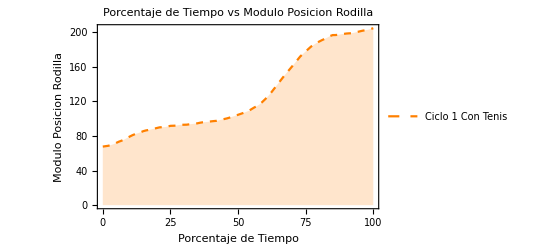

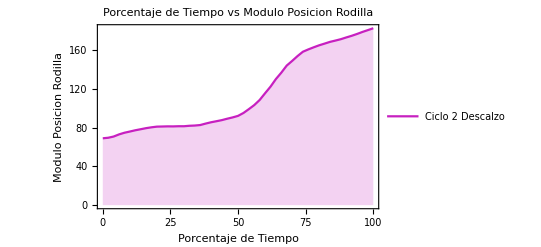

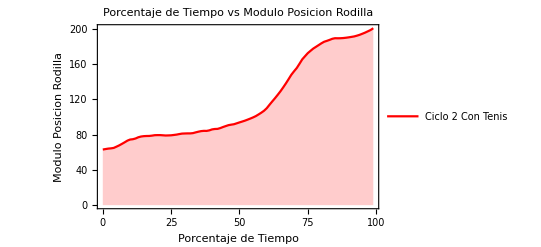

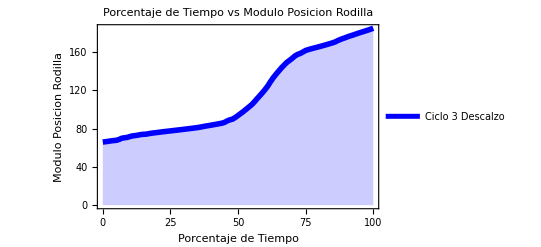

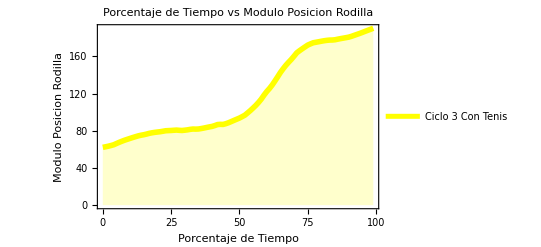

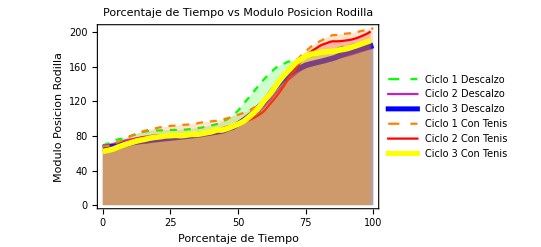

```mathematica
(*Importamos el archivo excel descalzo*)
e = Import["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Practicas\\Practica 3\\Valores juntos Descalzo.xlsx"][[1]];
(*Importamos el archivo excel Con tenis*)
a = Import["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Practicas\\Practica 3\\Valores juntos Tenis.xlsx"][[1]];
(*Medimos la longitud del arreglo para saber la duracion de los ciclos*)
LongitudDeArregloD = Length[e];
LongitudDeArregloT = Length[a];
(*Separamos cada componente de tobillo, rodilla y cadera en vectores, X, Y*)
(*Ciclo 1*)
PosicionRodillaEnX1D=Table[{e[[i,4]]},{i,2,LongitudDeArregloD-1}];
PosicionRodillaEnY1D=Table[{e[[i,5]]},{i,2,LongitudDeArregloD-1}];
PosicionRodillaEnX1T=Table[{a[[i,4]]},{i,2,LongitudDeArregloT-1}];
PosicionRodillaEnY1T=Table[{a[[i,5]]},{i,2,LongitudDeArregloT-1}];
(*Ciclo 2*)
PosicionRodillaEnX2D=Table[{e[[i,11]]},{i,2,LongitudDeArregloD-7}];
PosicionRodillaEnY2D=Table[{e[[i,12]]},{i,2,LongitudDeArregloD-7}];
PosicionRodillaEnX2T=Table[{a[[i,11]]},{i,2,LongitudDeArregloT-1}];
PosicionRodillaEnY2T=Table[{a[[i,12]]},{i,2,LongitudDeArregloT-1}];
(*Ciclo 3*)

PosicionRodillaEnX3D=Table[{e[[i,18]]},{i,2,LongitudDeArregloD-1}];
PosicionRodillaEnY3D=Table[{e[[i,19]]},{i,2,LongitudDeArregloD-1}];
PosicionRodillaEnX3T=Table[{a[[i,18]]},{i,2,LongitudDeArregloT-1}];
PosicionRodillaEnY3T=Table[{a[[i,19]]},{i,2,LongitudDeArregloT-1}];
(*Tambien extraigo el vector tiempo*)
Tiempo1D =Table[{e[[i,1]]},{i,2,LongitudDeArregloD-1}];
Tiempo2D =Table[{e[[i,8]]},{i,2,LongitudDeArregloD-7}];
Tiempo3D=Table[{e[[i,15]]},{i,2,LongitudDeArregloD-1}];
Tiempo1T=Table[{a[[i,1]]},{i,2,LongitudDeArregloT-1}];
Tiempo2T =Table[{a[[i,8]]},{i,2,LongitudDeArregloT-1}];
Tiempo3T=Table[{a[[i,15]]},{i,2,LongitudDeArregloT-1}];
(*Junto cada componente de la posicion en un vector para cada ciclo*)
VectorPosicionRodilla1D = Table[{PosicionRodillaEnX1D[[i,1]],PosicionRodillaEnY1D[[i,1]]},{i,1,LongitudDeArregloD-2}];
VectorPosicionRodilla2D = Table[{PosicionRodillaEnX2D[[i,1]],PosicionRodillaEnY2D[[i,1]]},{i,1,LongitudDeArregloD-8}];
VectorPosicionRodilla3D = Table[{PosicionRodillaEnX3D[[i,1]],PosicionRodillaEnY3D[[i,1]]},{i,1,LongitudDeArregloD-2}];
VectorPosicionRodilla1T = Table[{PosicionRodillaEnX1T[[i,1]],PosicionRodillaEnY1T[[i,1]]},{i,1,LongitudDeArregloT-2}];
VectorPosicionRodilla2T = Table[{PosicionRodillaEnX2T[[i,1]],PosicionRodillaEnY2T[[i,1]]},{i,1,LongitudDeArregloT-2}];
VectorPosicionRodilla3T = Table[{PosicionRodillaEnX3T[[i,1]],PosicionRodillaEnY3T[[i,1]]},{i,1,LongitudDeArregloT-2}];

(*Calculo los modulos del vector rodilla de cada ciclo*)
ModuloRodilla1D=Table[{Norm[VectorPosicionRodilla1D[[i]]]},{i,1,LongitudDeArregloD-2}];
ModuloRodilla2D=Table[{Norm[VectorPosicionRodilla2D[[i]]]},{i,1,LongitudDeArregloD-8}];
ModuloRodilla3D=Table[{Norm[VectorPosicionRodilla3D[[i]]]},{i,1,LongitudDeArregloD-2}];
ModuloRodilla1T=Table[{Norm[VectorPosicionRodilla1T[[i]]]},{i,1,LongitudDeArregloT-2}];
ModuloRodilla2T=Table[{Norm[VectorPosicionRodilla2T[[i]]]},{i,1,LongitudDeArregloT-2}];
ModuloRodilla3T=Table[{Norm[VectorPosicionRodilla3T[[i]]]},{i,1,LongitudDeArregloT-2}];
(*Junto el modulo del vector rodilla con el tiempo de su respectivo ciclo*)
TiempoVsModuloRodilla1D= Table[{Tiempo1D[[i,1]],ModuloRodilla1D[[i,1]]},{i,1,LongitudDeArregloD-2}];
TiempoVsModuloRodilla2D= Table[{Tiempo2D[[i,1]],ModuloRodilla2D[[i,1]]},{i,1,LongitudDeArregloD-8}];
TiempoVsModuloRodilla3D= Table[{Tiempo3D[[i,1]],ModuloRodilla3D[[i,1]]},{i,1,LongitudDeArregloD-2}];
TiempoVsModuloRodilla1T= Table[{Tiempo1T[[i,1]],ModuloRodilla1T[[i,1]]},{i,1,LongitudDeArregloT-2}];
TiempoVsModuloRodilla2T= Table[{Tiempo2T[[i,1]],ModuloRodilla2T[[i,1]]},{i,1,LongitudDeArregloT-2}];
TiempoVsModuloRodilla3T= Table[{Tiempo3T[[i,1]],ModuloRodilla3T[[i,1]]},{i,1,LongitudDeArregloT-2}];
(*Vamos a graficar como si el movimiento fuera de 0 a 100 para eso calculamos el incremento
con la cantidad final del tiempo menos la inicial entre 100*)
IncrementoD=(e[[LongitudDeArregloD-1,1]]-e[[2,1]])/100;
Incremento2D=(e[[LongitudDeArregloD-7,8]]-e[[2,8]])/100;
IncrementoT=(a[[LongitudDeArregloT-1,1]]-a[[2,1]])/100;
(*La interpolacion crea una funcion de la variable TiempoVsModuloRodilla en la que podemos evaluar la variable*)
PorcentajeDeTiempoVsModuloRodilla1D = Interpolation[TiempoVsModuloRodilla1D,InterpolationOrder->1];
PorcentajeDeTiempoVsModuloRodilla2D = Interpolation[TiempoVsModuloRodilla2D,InterpolationOrder->1];
PorcentajeDeTiempoVsModuloRodilla3D = Interpolation[TiempoVsModuloRodilla3D,InterpolationOrder->1];
PorcentajeDeTiempoVsModuloRodilla1T = Interpolation[TiempoVsModuloRodilla1T,InterpolationOrder->1];
PorcentajeDeTiempoVsModuloRodilla2T = Interpolation[TiempoVsModuloRodilla2T,InterpolationOrder->1];
PorcentajeDeTiempoVsModuloRodilla3T = Interpolation[TiempoVsModuloRodilla3T,InterpolationOrder->1];

(*Armamos una tabla nueva con el eje x en porcentaje y el eje Y con la funcion de interpolacion*)
TablaPorcentajeDeTiempoVsModuloRodilla1D =Table[{(i/IncrementoD),PorcentajeDeTiempoVsModuloRodilla1D[i]},{i,TiempoVsModuloRodilla1D[[1,1]],TiempoVsModuloRodilla1D[[LongitudDeArregloD-2,1]],IncrementoD}];
TablaPorcentajeDeTiempoVsModuloRodilla2D=Table[{(i/Incremento2D),PorcentajeDeTiempoVsModuloRodilla2D[i]},{i,TiempoVsModuloRodilla2D[[1,1]],TiempoVsModuloRodilla2D[[LongitudDeArregloD-8,1]],Incremento2D}];
TablaPorcentajeDeTiempoVsModuloRodilla3D=Table[{(i/IncrementoD),PorcentajeDeTiempoVsModuloRodilla3D[i]},{i,TiempoVsModuloRodilla3D[[1,1]],TiempoVsModuloRodilla3D[[LongitudDeArregloD-2,1]],IncrementoD}];
TablaPorcentajeDeTiempoVsModuloRodilla1T =Table[{(i/IncrementoT),PorcentajeDeTiempoVsModuloRodilla1T[i]},{i,TiempoVsModuloRodilla1T[[1,1]],TiempoVsModuloRodilla1T[[LongitudDeArregloT-2,1]],IncrementoT}];
TablaPorcentajeDeTiempoVsModuloRodilla2T=Table[{(i/IncrementoT),PorcentajeDeTiempoVsModuloRodilla2T[i]},{i,TiempoVsModuloRodilla2T[[1,1]],TiempoVsModuloRodilla2T[[LongitudDeArregloT-2,1]],IncrementoT}];
TablaPorcentajeDeTiempoVsModuloRodilla3T=Table[{(i/IncrementoT),PorcentajeDeTiempoVsModuloRodilla3T[i]},{i,TiempoVsModuloRodilla3T[[1,1]],TiempoVsModuloRodilla3T[[LongitudDeArregloT-2,1]],IncrementoT}];

(*Graficamos el Ciclo 1*)
GraficaCiclo1CompletoD=ListPlot[{TablaPorcentajeDeTiempoVsModuloRodilla1D},Joined->True,Filling->Axis,PlotStyle->{{Green,Glow,Dashed}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Posicion Rodilla"},PlotLegends->{"Ciclo 1 Descalzo"},PlotLabel->"Porcentaje de Tiempo vs Modulo Posicion Rodilla"]
GraficaCiclo1CompletoT=ListPlot[{TablaPorcentajeDeTiempoVsModuloRodilla1T},Joined->True,Filling->Axis,PlotStyle->{{Orange,Glow,Dashed}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Posicion Rodilla"},PlotLegends->{"Ciclo 1 Con Tenis"},PlotLabel->"Porcentaje de Tiempo vs Modulo Posicion Rodilla"]
(*Graficamos el Ciclo 2*)
GraficaCiclo2CompletoD=ListPlot[{TablaPorcentajeDeTiempoVsModuloRodilla2D},Joined->True,Filling->Axis,PlotStyle->{{Purple,Glow,Hue[0.84,0.84,0.78]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Posicion Rodilla"},PlotLegends->{"Ciclo 2 Descalzo"},PlotLabel->"Porcentaje de Tiempo vs Modulo Posicion Rodilla"]
GraficaCiclo2CompletoT=ListPlot[{TablaPorcentajeDeTiempoVsModuloRodilla2T},Joined->True,Filling->Axis,PlotStyle->{{Red,Glow}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Posicion Rodilla"},PlotLegends->{"Ciclo 2 Con Tenis"},PlotLabel->"Porcentaje de Tiempo vs Modulo Posicion Rodilla"]
(*Graficamos el Ciclo 3*)
GraficaCiclo3CompletoD=ListPlot[{TablaPorcentajeDeTiempoVsModuloRodilla3D},Joined->True,Filling->Axis,PlotStyle->{{Blue,Glow,Thickness[0.01]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Posicion Rodilla"},PlotLegends->{"Ciclo 3 Descalzo"},PlotLabel->"Porcentaje de Tiempo vs Modulo Posicion Rodilla"]
GraficaCiclo3CompletoT=ListPlot[{TablaPorcentajeDeTiempoVsModuloRodilla3T},Joined->True,Filling->Axis,PlotStyle->{{Yellow,Glow,Thickness[0.01]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Posicion Rodilla"},PlotLegends->{"Ciclo 3 Con Tenis"},PlotLabel->"Porcentaje de Tiempo vs Modulo Posicion Rodilla"]
(*Graficamos los tres Ciclos en una sola grafica*)

Show[{GraficaCiclo1CompletoD,GraficaCiclo2CompletoD,GraficaCiclo3CompletoD,GraficaCiclo1CompletoT,GraficaCiclo2CompletoT,GraficaCiclo3CompletoT},PlotRange->All]
```